### Wprowadzenie wartosci dla czasu zycia mionu w ukladzie spoczynkowym (zwiazanym z mionem) ("τ_o") oraz dla predkosci swiatla w prozni.

```mathematica
ClearAll["Global`*"];
```

```mathematica
τo=2.6×10^-8;   (* s *)
```

```mathematica
c=3×10^8;             (* m/s *)
```

### Wprowadzenie wzoru na czasu zycia mionu w ukladzie zwiazanym z Ziemia ("τ"). Symbol "v" oznacza predkosc mionu mierzona wzgledem Ziemi.

```mathematica
τ=τo/(√(1-v^2/c^2));
```

### Wprowadzenie wzorow na zasieg mionu liczony klasycznie ("S_k[v_]") i relatywistycznie ("S_r[v_]").

```mathematica
Sk[v_]=v×τo;
Sr[v_]=v×τ;
```

### Sporzadzenie wykresu obrazujacego zaleznosc zasiegu mionu liczonego klasycznie od predkosci mionu mierzonej wzgledem Ziemi.

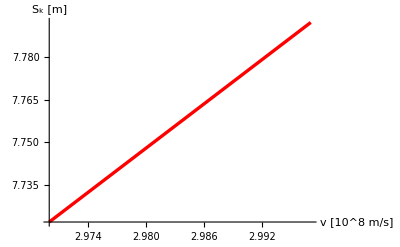

```mathematica
Plot[Sk[v×10^8],{v,0.990×c×10^-8,0.999×c×10^-8},
TextStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
 PlotStyle->{{RGBColor[1,0,0],Thickness[0.006]}},
AxesLabel->{"v [10^8 m/s]","S_k  [m]"}]
```

### Sporzadzenie wykresu obrazujacego zaleznosc zasiegu mionu liczonego relatywistycznie od predkosci mionu mierzonej wzgledem Ziemi.

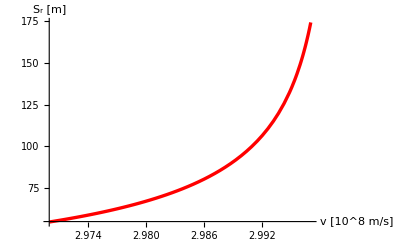

```mathematica
Plot[Sr[v×10^8],{v,0.990×c×10^-8,0.999×c×10^-8},
TextStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
 PlotStyle->{{RGBColor[1,0,0],Thickness[0.006]}},
AxesLabel->{"v [10^8 m/s]","S_r  [m]"}]
```